```mathematica
Quit[]
```

### Geometry

```mathematica
n=4
```

4

```mathematica
coord={r,θ,ϕ,t}
```

{r,θ,ϕ,t}

```mathematica
metric={{A[r,t]^2,0,0,0},{0,B[r,t]^2 r^2,0,0},{0,0,B[r,t]^2 r^2 Sin[θ]^2,0},{0,0,0,-1}}
```

{{A[r,t]^2,0,0,0},{0,r^2 B[r,t]^2,0,0},{0,0,r^2 B[r,t]^2 Sin[θ]^2,0},{0,0,0,-1}}

```mathematica
metric//MatrixForm
```

(A[r,t]^2 | 0 | 0 | 0
0 | r^2 B[r,t]^2 | 0 | 0
0 | 0 | r^2 B[r,t]^2 Sin[θ]^2 | 0
0 | 0 | 0 | -1)

```mathematica
Det[metric]
```

-r^4 A[r,t]^2 B[r,t]^4 Sin[θ]^2

```mathematica
inversemetric=Simplify[Inverse[metric]]
```

{{1/A[r,t]^2,0,0,0},{0,1/(r^2 B[r,t]^2),0,0},{0,0,Csc[θ]^2/(r^2 B[r,t]^2),0},{0,0,0,-1}}

```mathematica
inversemetric//MatrixForm
```

(1/A[r,t]^2 | 0 | 0 | 0
0 | 1/(r^2 B[r,t]^2) | 0 | 0
0 | 0 | Csc[θ]^2/(r^2 B[r,t]^2) | 0
0 | 0 | 0 | -1)

```mathematica
affine:=affine=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coord[[k]]]+D[metric[[s,k]],coord[[j]]]-D[metric[[j,k]],coord[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
```

```mathematica
listaffine:=Table[If[UnsameQ[affine[[i,j,k]],0],{ToString[Γ[i,j,k]],affine[[i,j,k]]}],{i,1,n},{j,1,n},{k,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listaffine],Null],2],TableSpacing->{2,2}]
```

Γ[1, 1, 1] | (A^(1,0)[r,t])/A[r,t]
Γ[1, 2, 2] | -(r B[r,t] (B[r,t]+r B^(1,0)[r,t]))/A[r,t]^2
Γ[1, 3, 3] | -(r B[r,t] Sin[θ]^2 (B[r,t]+r B^(1,0)[r,t]))/A[r,t]^2
Γ[1, 4, 1] | (A^(0,1)[r,t])/A[r,t]
Γ[2, 2, 1] | 1/r+(B^(1,0)[r,t])/B[r,t]
Γ[2, 3, 3] | -Cos[θ] Sin[θ]
Γ[2, 4, 2] | (B^(0,1)[r,t])/B[r,t]
Γ[3, 3, 1] | 1/r+(B^(1,0)[r,t])/B[r,t]
Γ[3, 3, 2] | Cot[θ]
Γ[3, 4, 3] | (B^(0,1)[r,t])/B[r,t]
Γ[4, 1, 1] | A[r,t] A^(0,1)[r,t]
Γ[4, 2, 2] | r^2 B[r,t] B^(0,1)[r,t]
Γ[4, 3, 3] | r^2 B[r,t] Sin[θ]^2 B^(0,1)[r,t]

```mathematica
riemann:=riemann=Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[s,j,l]]affine[[i,k,s]]-affine[[s,j,k]]affine[[i,l,s]],{s,1,n}],{i,1,n},{j,1,n},{k,1,n},{l,1,n}]]
```

```mathematica
listriemann:=Table[If[UnsameQ[riemann[[i,j,k,l]],0],{ToString[R[i,j,k,l]],riemann[[i,j,k,l]]}],{i,1,n},{j,1,n},{k,1,n},{l,1,k-1}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listriemann],Null],2],TableSpacing->{2,2}]
```

R[1, 2, 2, 1] | -(r B[r,t] (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
R[1, 2, 4, 2] | (r B[r,t] (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]^3
R[1, 3, 3, 1] | -(r B[r,t] Sin[θ]^2 (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
R[1, 3, 4, 3] | (r B[r,t] Sin[θ]^2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]^3
R[1, 4, 4, 1] | (A^(0,2)[r,t])/A[r,t]
R[2, 1, 2, 1] | (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t]))/(r A[r,t] B[r,t])
R[2, 1, 4, 2] | (-B[r,t] A^(0,1)[r,t]-r A^(0,1)[r,t] B^(1,0)[r,t]+A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[2, 3, 3, 2] | Sin[θ]^2 (-1-r^2 (B^(0,1)[r,t])^2+((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2)
R[2, 4, 2, 1] | (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[2, 4, 4, 2] | (B^(0,2)[r,t])/B[r,t]
R[3, 1, 3, 1] | (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t]))/(r A[r,t] B[r,t])
R[3, 1, 4, 3] | (-B[r,t] A^(0,1)[r,t]-r A^(0,1)[r,t] B^(1,0)[r,t]+A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[3, 2, 3, 2] | 1+r^2 (B^(0,1)[r,t])^2-((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2
R[3, 4, 3, 1] | (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t]))/(r A[r,t] B[r,t])
R[3, 4, 4, 3] | (B^(0,2)[r,t])/B[r,t]
R[4, 1, 4, 1] | A[r,t] A^(0,2)[r,t]
R[4, 2, 2, 1] | (r B[r,t] (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]
R[4, 2, 4, 2] | r^2 B[r,t] B^(0,2)[r,t]
R[4, 3, 3, 1] | (r B[r,t] Sin[θ]^2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/A[r,t]
R[4, 3, 4, 3] | r^2 B[r,t] Sin[θ]^2 B^(0,2)[r,t]

```mathematica
ricci:=ricci=Simplify[Table[Sum[riemann[[i,j,i,l]],{i,1,n}],{j,1,n},{l,1,n}]]
```

```mathematica
listricci:=Table[If[UnsameQ[ricci[[j,l]],0],{ToString[R[j,l]],ricci[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listricci],Null],2],TableSpacing->{2,2}]
```

R[1, 1] | A[r,t] A^(0,2)[r,t]+(2 (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/(r A[r,t] B[r,t])
R[2, 2] | 1+r^2 (B^(0,1)[r,t])^2+r^2 B[r,t] B^(0,2)[r,t]-((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2+(r B[r,t] (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
R[3, 3] | Sin[θ]^2 (1+r^2 (B^(0,1)[r,t])^2+r^2 B[r,t] B^(0,2)[r,t]-((B[r,t]+r B^(1,0)[r,t])^2)/A[r,t]^2+(r B[r,t] (r A[r,t]^2 A^(0,1)[r,t] B^(0,1)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3)
R[4, 1] | (2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/(r A[r,t] B[r,t])
R[4, 4] | -(A^(0,2)[r,t])/A[r,t]-(2 B^(0,2)[r,t])/B[r,t]

```mathematica
scalar=Simplify[Sum[inversemetric[[i,j]]ricci[[i,j]],{i,1,n},{j,1,n}]]
```

1/(r^2 A[r,t]^3 B[r,t]^2)2 (r^2 A[r,t]^2 B[r,t] (2 A^(0,1)[r,t] B^(0,1)[r,t]+B[r,t] A^(0,2)[r,t])+A[r,t]^3 (1+r^2 (B^(0,1)[r,t])^2+2 r^2 B[r,t] B^(0,2)[r,t])+2 r B[r,t] A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (B[r,t]^2+r^2 (B^(1,0)[r,t])^2+2 r B[r,t] (3 B^(1,0)[r,t]+r B^(2,0)[r,t])))

```mathematica
einstein:=einstein=Simplify[ricci-(1/2)scalar*metric]
```

```mathematica
listeinstein:=Table[If[UnsameQ[einstein[[j,l]],0],{ToString[G[j,l]],einstein[[j,l]]}],{j,1,n},{l,1,j}]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listeinstein],Null],2],TableSpacing->{2,2}]
```

G[1, 1] | (-A[r,t]^2 (1+r^2 (B^(0,1)[r,t])^2+2 r^2 B[r,t] B^(0,2)[r,t])+(B[r,t]+r B^(1,0)[r,t])^2)/(r^2 B[r,t]^2)
G[2, 2] | -(r B[r,t] (r A[r,t]^2 (A^(0,1)[r,t] B^(0,1)[r,t]+B[r,t] A^(0,2)[r,t])+r A[r,t]^3 B^(0,2)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
G[3, 3] | -(r B[r,t] Sin[θ]^2 (r A[r,t]^2 (A^(0,1)[r,t] B^(0,1)[r,t]+B[r,t] A^(0,2)[r,t])+r A[r,t]^3 B^(0,2)[r,t]+A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (2 B^(1,0)[r,t]+r B^(2,0)[r,t])))/A[r,t]^3
G[4, 1] | (2 (B[r,t] A^(0,1)[r,t]+r A^(0,1)[r,t] B^(1,0)[r,t]-A[r,t] (B^(0,1)[r,t]+r B^(1,1)[r,t])))/(r A[r,t] B[r,t])
G[4, 4] | (2 r^2 A[r,t]^2 B[r,t] A^(0,1)[r,t] B^(0,1)[r,t]+A[r,t]^3 (1+r^2 (B^(0,1)[r,t])^2)+2 r B[r,t] A^(1,0)[r,t] (B[r,t]+r B^(1,0)[r,t])-A[r,t] (B[r,t]^2+r^2 (B^(1,0)[r,t])^2+2 r B[r,t] (3 B^(1,0)[r,t]+r B^(2,0)[r,t])))/(r^2 A[r,t]^3 B[r,t]^2)

### Static

```mathematica
StaticEoM={-f''[x]-2/x f'[x]+(2f[x])/x^2+f[x](f[x]^2-1)==0};
```

```mathematica
xi=10^-2;
xf=10;
```

```mathematica
BC={f[xi]==0,f'[xi]==1.518053};
```

```mathematica
StaticSol=NDSolve[Join[StaticEoM,BC],f[x],{x,xi,xf}][[1]];
```

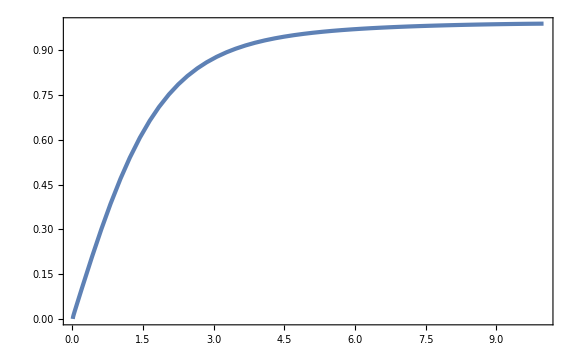

```mathematica
Plot[f[x]/.StaticSol,{x,xi,xf},PlotRange->Full]
```

```mathematica
BC={f[xi]==0,f[xf]==1};
```

```mathematica
StaticSol=NDSolve[Join[StaticEoM,BC],f[x],{x,xi,xf},Method->{"Shooting","StartingInitialConditions"->{f[xi]==0,f'[xi]==1.518053}}][[1]];
```

```mathematica
fsol[x_]=f[x]/.StaticSol;
```

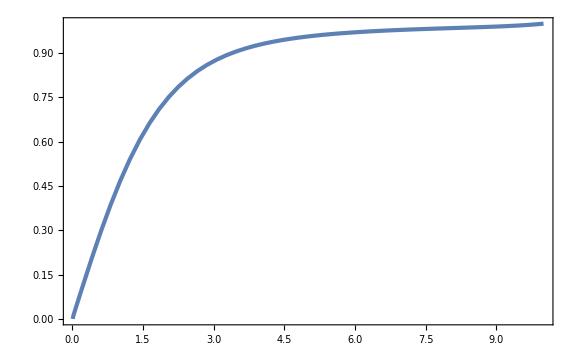

```mathematica
Plot[fsol[x],{x,xi,xf},PlotRange->Full]
```

### Vacuum

```mathematica
K11[x_,t_]=-D[A[x,t], t]/A[x,t];
K22[x_,t_]=-D[B[x,t], t]/B[x,t];
KK[x_,t_]=K11[x,t]+2K22[x,t];
```

```mathematica
tf=10;
```

```mathematica
G00={K22[x,t](2KK[x,t]-3K22[x,t])-2 D[B[x,t], x]/(A[x,t]^2 B[x,t])-(D[B[x,t], x])^2/(A[x,t]^2 B[x,t]^2)+2((D[A[x,t], x])(D[B[x,t], x]))/(A[x,t]^3 B[x,t])-6 D[B[x,t], x]/(A[x,t]^2 B[x,t]x)+2 D[A[x,t], x]/(A[x,t]^3 x)-1/(A[x,t]^2 x^2)+1/(B[x,t]^2 x^2)==8π η^2((D[Φ[x,t], t])^2/2+(D[Φ[x,t], x])^2/(2 A[x,t]^2)+Φ[x,t]^2/(B[x,t]^2 x^2)+1/4(Φ[x,t]^2-1)^2)};
G01={D[K22[x,t], x]+(D[B[x,t], x]/B[x,t]+1/x)(3K22[x,t]-KK[x,t])==4π η^2 D[Φ[x,t], t]D[Φ[x,t], x]};
Gtr={D[KK[x,t], t]-K11[x,t]^2-2 K22[x,t]^2==8π η^2((D[Φ[x,t], t])^2-1/4(Φ[x,t]^2-1)^2)};
EoM={D[D[Φ[x,t], t], t]-KK[x,t]D[Φ[x,t], t]-D[D[Φ[x,t], x], x]/A[x,t]^2-(-D[A[x,t], x]/A[x,t]+2 D[B[x,t], x]/B[x,t]+2/x)D[Φ[x,t], x]/A[x,t]^2+(2Φ[x,t])/(B[x,t]^2 x^2)+Φ[x,t](Φ[x,t]^2-1)==0};
```

```mathematica
ICBC={Φ[x,0]==fsol[x],D[Φ[x,t], t]==0/.{t->0},A[x,0]==1,B[x,0]==1,K22[x,0]==-η/Sqrt[3]Sqrt[fsol'[x]^2/2+fsol[x]^2/x^2+1/4(fsol[x]^2-1)^2],KK[x,0]==-(3η)/Sqrt[3]Sqrt[fsol'[x]^2/2+fsol[x]^2/x^2+1/4(fsol[x]^2-1)^2],Φ[xi,t]==0,D[Φ[x,t], x]==fsol'[x]/.{x->xi},KK[xi,t]==3K22[xi,t]}//Simplify;
```

```mathematica
NDSolve[Join[G01,Gtr,EoM,ICBC]/.{η->0.1},{Φ[x,t],A[x,t],B[x,t]},{x,xi,xf},{t,0,tf}]
```

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.